-Graphics3D-

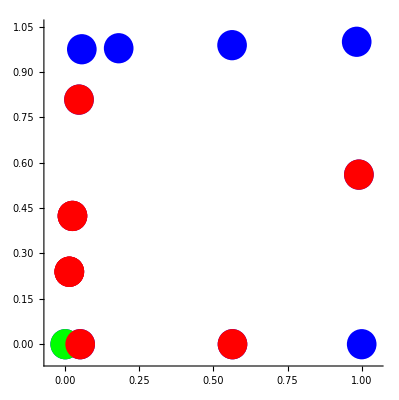

```mathematica
sr=0.05;
points=
{
{-0.508944,-0.0709977,1},{-0.993693,-0.183432,1},{0.0625277,0.0615507,1},{0.118568,0.0745488,1},{-0.993329,-0.137179,0.447877},{-0.993044,-0.10096,0.0155265},{0.0386722,0.136305,0.0398471},{-0.099687,0.104486,0.0365856},{-0.5253,0.00660723,0.0265526},{0.0523104,0.125763,0.203746},{0.0838186,0.101409,0.582398},{0.0989288,0.0897287,0.763986}
};
aufpunkt ={-0.508944,-0.0709977,1};
ersterpfeil={-0.97414,-0.225945,0};
zweiterpfeil={-0.018344,0.0790883,-0.996699};
neueraufpunkt={0.118568,0.0745488,1};
ersterbounding={0.135379,0.0851189,1.14179};
zweiterbounding={-0.962193,-0.223173,0};
texcoords=
{
{0.564176,0},
{1,0},
{0.0503838,0},
{0,0},
{0.990536,0.560831},
{0.983126,1},
{0.0559438,0.975294},
{0.180284,0.978605},
{0.562774,0.988798},
{0.0463941,0.808812},
{0.0243317,0.424188},
{0.0137514,0.239733}
};
minimalpunkt={0,0};
deletedtexcoords=
{
{0.0137514,0.239733},{0.0137514,0.239733},{0.0137514,0.239733},{0.0243317,0.424188},{0.0243317,0.424188},{0.0463941,0.808812},{0.564176,1.20782 10^-6},{0.0503838,-9.29092 10^-8},{0.990536,0.560831}
};
sortedpoints=
{
{0.118568,0.0745488,1},{-0.993044,-0.10096,0.0155265},{-0.993693,-0.183432,1}
};
Graphics3D[
{
Blue,
Map[Sphere[#1,sr]&,points],
(*
Blue,
Arrow[{aufpunkt,aufpunkt + ersterpfeil}],
Arrow[{aufpunkt,aufpunkt + zweiterpfeil}],
Green,
Arrow[{neueraufpunkt,neueraufpunkt + ersterpfeil}],
Arrow[{neueraufpunkt,neueraufpunkt + zweiterpfeil}],
Red,
Arrow[{neueraufpunkt,neueraufpunkt + ersterbounding}],
Arrow[{neueraufpunkt,neueraufpunkt + zweiterbounding}],*)
Black,
Line[sortedpoints],
Map[Text[#1,#1]&,sortedpoints]
},
Boxed->False
]

Graphics[
{
Blue,
Map[Disk[#1,sr]&,texcoords],
Green,
Disk[minimalpunkt,sr],
Red,
Map[Disk[#1,sr]&,deletedtexcoords]
},
Axes->True
]
```